# Define functions and module for general ODE

```mathematica
ρi = 0.5;(*ratio of ice/rock density*)
bv = bmax*(x^2-1);(* quadratic basal topography*)
eqiceODE = (ρ-1)(D[H[x],x]+D[bv,x]) - 0.5*((α-D[bv,x])/(1+(D[bv,x])^2)*D[bv,x,x]/(1+D[bv,x]*α))*H[x]  -ρ*((Abs[b0]-b0) - H[x]-bv+ x*α)*(fλ/H[x]+D[bv,x,x]*(α/(1+D[bv,x]*α)-D[bv,x]/ (1+(D[bv,x])^2)))==fλ + ρ *α-(α-D[bv,x])/(1+D[bv,x]*α);
eqiceODE/.bmax->b0
xPosRoot[ρv_?NumericQ,αv_?NumericQ,fv_?NumericQ, b0_?NumericQ]:=Module[{sol,res},
xend=5.0;sol=Quiet@Check[NDSolve[{eqiceODE/.{ρ->ρv,bmax->b0,α->αv,fλ->fv},H[0]==Abs[b0],WhenEvent[H[x]<=0.0000001,{xend=x,"StopIntegration"}]},H,{x,0,1}],$Failed];
If[sol===$Failed,0,(*fallback if solve fails*)
res=xend
]
]
```

-ρ (-0.2 ((0.2 x)/(1+0.04 x^2)+α/(1-0.2 x α))+fλ/H[x]) (0.2+0.1 (-1+x^2)+x α-H[x])+(0.1 (0.2 x+α) H[x])/((1+0.04 x^2) (1-0.2 x α))+(-1+ρ) (-0.2 x+H'[x])==fλ-(0.2 x+α)/(1-0.2 x α)+α ρ

## Insert values for a test case

0.0917926

0.0917926

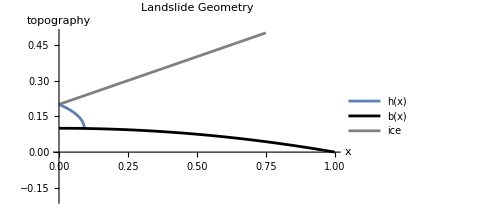

```mathematica
αv=0.4;
fv=0.45;
b0=-0.1;
xPosRoot[ρi,αv,fv,b0]
xendice=1.0;
solice = NDSolve[{eqiceODE/.{ρ->ρi,bmax->b0,α->αv,fλ->fv},H[0]==Abs[b0],WhenEvent[H[x]<=0.0000001,{xendice=x,"StopIntegration"}]},H,{x,0,1.0}];
xendice
(*thickness has artifacts*)
Hsol= H[x]/.solice;
Hice[x_]:=Piecewise[{{Evaluate[Hsol],0<=x<=xendice }},0]
Plot[{Hice[x]+bv/.bmax->b0,bv/.bmax->b0,(Abs[b0]-b0)+x*αv},{x,0,1},PlotStyle->{DarkBlue,Black,Gray},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","b(x)","ice"},ImageSize->Medium,PlotRange->{-0.2,0.5}]
```

## Define locus function and plot stability criteria

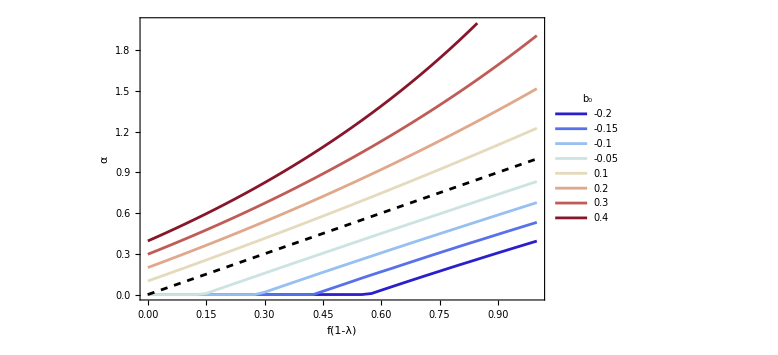

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideIceToeTrueStabilityBoundaryPlot_rho0.jpg

```mathematica
locusfun[ρ_,f_,b0_]:=Module[{res},res=Quiet@FindRoot[xPosRoot[ρ,αsol,f,b0]==1.0,{αsol,0.0,0,10}];
αsol/. res]
bvals=Join[{-0.2,-0.15,-0.1,-0.05},Subdivide[0.1,0.4,3]];
roundedLabels = Round[bvals,0.01];
fvals=Range[0,1,0.025];  

(*Parallel computation of {f,alpha} pairs for each ρ,b value*)
ρvalue=0;
data=ParallelTable[{f,locusfun[ρvalue,f,b]},{b,bvals},{f,fvals}];

(*Plot each set of points as a line*)
p1=ListLinePlot[data,PlotRange->{0,2},PlotLegends->Placed[LineLegend[roundedLabels,LegendLabel->Style["b₀",Bold,18]],Right],LabelStyle->{FontSize->18},ImageSize->Large,PlotStyle->ColorData["ThermometerColors"]/@Rescale[Range[Length[bvals]]]];
p2=Plot[f,{f,0,1},PlotStyle->{Black,Dashed}];
fig=Show[p1,p2,FrameLabel->{"f(1-λ)","α"},Frame->True,LabelStyle->{FontSize->18}]
Export[NotebookDirectory[]<>"LandslideIceToeTrueStabilityBoundaryPlot_rho"<>ToString[ρvalue]<>".jpg",fig,"JPEG"]
```